```mathematica
ResourceFunction["MaTeXInstall"][]
```

Paclet[MaTeX,1.7.8,<>]

## Q 1 Q2 integrated profiles vs t

```mathematica
<<MaTeX`
A=Import["~/Programs/Folded_XXZ_GS/Data/UUD/Q2_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)
timestep=0.1;
TimeSlice0=10;
TimeSlice1=10timestep;
TimeSlice2=25/timestep;
TimeSlice3=60/timestep;

radius=5;
widht=Thickness[0.2];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];
```

Import::nffil: File ~/Programs/Folded_XXZ_GS/Data/UUD/Q2_profile.dat not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,1].

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

```mathematica
(*RUN this part also*)
Qexpectation[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
(*To change Subscript[Q, 1]^- -> Subscript[Q, 1]^+ one should change 3->2 below*)
Obs[n_,time_]:=Qexpectation[n,2,time];
FIG=ListPlot[{
Table[ {TimeSlice, Sum[Obs[n,TimeSlice/timestep],{n,xmin,xmax}]
} ,{TimeSlice,0,timestep TimeSlice3,timestep}]
(*,Avalanche*)
(*,Table[
{TimeSlice, Sum[Obs2[n,TimeSlice],{n,xmin,xmax}]} ,{TimeSlice,0, TimeSlice3,1}]*)
},
Joined->False
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"t","\\sum_x \\mathcal{Q}^{\\pm}_{x}(t)"},FontSize->16]
,LabelStyle->Directive[FontSize->12]
,LABELS={
"t="<>ToString[TimeSlice3*timestep]
,"\\sigma^x(t="<>ToString[TimeSlice1]<>")"
};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 12],{1.0,0.6}]
,PlotRange->{{0,TimeSlice3 timestep},{Automatic,Automatic}}
,PlotMarkers->{
{BLUE0,radius},
{RED0, radius}
}
 ]
```

-Graphics-

## Q 1 Q2 averaged profiles

```mathematica
<<MaTeX`
A=Import["~/Programs/Folded_XXZ_GS/Data/UUD/Q1_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)

radius=5;
widht=Thickness[0.2];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];
```

Import::nffil: File ~/Programs/Folded_XXZ_GS/Data/UUD/Q1_profile.dat not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,1].

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

```mathematica
(*RUN this part also*)
timestep=0.1;
TimeSlice0=10;
TimeSlice1=10/timestep;
TimeSlice2=25/timestep;
TimeSlice3=60/timestep;


Qexpectation[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
(*To change Subscript[Q, 1]^- -> Subscript[Q, 1]^+ one should change 3->2 below*)
Obs[n_,time_]:=time^1Qexpectation[n,3,time];

AvrgData={};
AverWindow =3;
TimeSlice=TimeSlice3;
For[l=xmin, l<xmax, l+=AverWindow,{
average = 0;
counter=0;
For[l0=0,l0<AverWindow,l0++,{
If[l0+l>xmax, {Break[]}];
obs=Obs[l+l0,TimeSlice];
(*If[Abs[obs]>10^-6,*)
average +=obs;
counter++;
;

}];
If[counter==0,counter++];
average /=counter;
AppendTo[AvrgData,{(l+Floor[AverWindow/2]-Floor[(xmax-xmin)/2]-2)/(TimeSlice*timestep),average}];
}]

FIG=ListPlot[{
Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+0,xmax,3}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+1,xmax,3}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+2,xmax,3}]
(*,Table[{(A[[n+SystemSize*Floor[TimeSlice1],1]]+SHIFT)/(TimeSlice1*timestep),Obs[n,TimeSlice1]},{n,xmin,xmax}]*)
(*,AvrgData*)
(*,{0} *)(*This is technical thing to match plot frame boxes with other plots
I add it to use legenda sigma^x ...
*)
},
Joined->True
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"\\ell/t","t\\mathcal{Q^-}_1(\\ell/t)"},FontSize->16]
,LabelStyle->Directive[FontSize->12]
,LABELS={
"0mod3; t="<>ToString[TimeSlice3*timestep]
(*,"Avrg Over "<>ToString[AverWindow]<>"Sites"*)
(*,"t="<>ToString[TimeSlice2*timestep]*)
,"1mod3; t="<>ToString[TimeSlice3*timestep]
,"2mod3; t="<>ToString[TimeSlice3*timestep]
(*,"\\sigma^x(t="<>ToString[TimeSlice1]<>")"*)

};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 12],{1.0,0.6}]
,PlotRange->{{-7,7},{-12,12}}
,PlotMarkers->{
{BLUE0,radius},
{RED0, radius},
{GREEN0, radius}
}
 ]
```

-Graphics-

```mathematica
Averaging[window_,{
AvrgData={};
AverWindow =window;
TimeSlice=TimeSlice3;
For[l=xmin, l<xmax, l+=AverWindow,{
average = 0;
counter=0;
For[l0=0,l0<AverWindow,l0++,{
If[l0+l>xmax, {Break[]}];
obs=Obs[l+l0,TimeSlice];
If[Abs[obs]>10^-6,
{average +=obs;
counter++;
}];

}];
If[counter==0,counter++];
average /=counter;
AppendTo[AvrgData,{(l+Floor[AverWindow/2]-Floor[(xmax-xmin)/2]-2)/(TimeSlice*timestep),average}];
}];
Return AvrgData;
}]
```

Averaging[window_,{Null}]

## {(S^z)_(3l+a)(t)} UUD profile

```mathematica
A=Import["~/Programs/Folded_XXZ_GS/Data/UUD/SxSySz_profile.dat"];
A=Drop[A,1];
𝔸=DeleteCases[A,_?(Length[#]<4&)];
A=Chop[𝔸[[;;,{1,2,3,4}]]]; (*l, Subscript[σ^x, l], (σ^y)_(l,)Subscript[σ^z, l]*)
(*A=Cases[A,_?(Mod[#[[1]],2]==0&)];*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize;
timestep=0.1;
<<MaTeX`;
TimeSlice1 = 10/timestep;
TimeSlice2 = 60/timestep;
SHIFT=1;
(*technical part:  point types etc *)
radius=10;
widht=Thickness[0];
CircleEdgeWidht=Thickness[0.15];


RED0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,Disk[]}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];

everypoint=3;

P[l_,time_,col_]:=A[[l+SystemSize*Floor[time],col]];
Obs[l_,time_]:=  P[l,time,2];
FIG=ListPlot[{
  (*  Table[{(P[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep), 2P[l,TimeSlice1,4]},{l,xmin,xmax,everypoint}]*)
Table[{(P[l,TimeSlice2,1]+SHIFT)/(TimeSlice2*timestep), 2P[l,TimeSlice2,4]},{l,xmin,xmax,everypoint}]

(* ,Table[{(P[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep), 2P[l,TimeSlice1,4]},{l,xmin+1,xmax,everypoint}]*),Table[{(P[l,TimeSlice2,1]+SHIFT)/(TimeSlice2*timestep), 2P[l,TimeSlice2,4]},{l,xmin+1,xmax,everypoint}]

(*,Table[{(P[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep), 2P[l,TimeSlice1,4]},{l,xmin+2,xmax,everypoint}]*),Table[{(P[l,TimeSlice2,1]+SHIFT)/(TimeSlice2*timestep), 2P[l,TimeSlice2,4]},{l,xmin+2,xmax,everypoint}]

},
PlotRange->{{-10.5,10.5},{Automatic,Automatic}},
(*AxesLabel -> {"x/t","Spin operator"},*)(*PlotLegends->{"Sx, t="<>ToString[TimeSlice/10],"Sy","Sz"},*)
PlotStyle->PointSize[Medium],

Joined->False,
Frame->True,
FrameStyle->BlackFrame,
Axes->{False,False},
BaseStyle->{FontFamily->"Latin Modern Roman"},
FrameLabel->MaTeX[{"\\ell/t","\\sigma^z_{\\ell}"},FontSize->16],
LabelStyle->Directive[FontSize->12],
PlotLegends->{Placed[MaTeX[{
(*"\\sigma^z_{3\\ell}(t="<>ToString[TimeSlice1*timestep]<>")",*)
"\\sigma^z_{3\\ell}(t="<>ToString[TimeSlice2*timestep]<>")",

(*"\\sigma^z_{3\\ell+1}(t="<>ToString[TimeSlice1*timestep]<>")",*)
"\\sigma^z_{3\\ell+1}(t="<>ToString[TimeSlice2*timestep]<>")",

(*"\\sigma^z_{3\\ell+2}(t="<>ToString[TimeSlice1*timestep]<>")",*)
"\\sigma^z_{3\\ell+2}(t="<>ToString[TimeSlice2*timestep]<>")"


},FontSize->12],{1.,0.6}]}
(*,FrameTicks->{
{{0,0.1,0.2,0.3},None},
{{-6,-4,-2,0,2,4,6},None}}*)

,PlotMarkers->{
{GREEN0,radius}
,{BLUE0,radius}
,{RED0, radius}
(*,{BLUE,radius}*)

(*,{BLUE0,radius}*)
(*,{RED1,radius}*)

(*,{BLACK,0.008},{BLACK,0.008}*)
}

 ]
```

Import::nffil: File ~/Programs/Folded_XXZ_GS/Data/UUD/SxSySz_profile.dat not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,1].

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

-Graphics-

## S^vN profiles

```mathematica
<<MaTeX`
A=Import["~/Programs/Folded_XXZ_GS/Data/UUD/Entropy_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)

radius=5;
widht=Thickness[0.2];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];
```

Import::nffil: File ~/Programs/Folded_XXZ_GS/Data/UUD/Entropy_profile.dat not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,1].

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

```mathematica
(*RUN this part also*)
timestep=0.1;
TimeSlice0=10;
TimeSlice1=10/timestep;
TimeSlice2=25/timestep;
TimeSlice3=60/timestep;


Qexpectation[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
(*To change Subscript[Q, 1]^- -> Subscript[Q, 1]^+ one should change 3->2 below*)
Obs[n_,time_]:=Qexpectation[n,2,time];

AvrgData={};
AverWindow =1;
TimeSlice=TimeSlice3;
For[l=xmin, l<xmax, l+=AverWindow,{
average = 0;
counter=0;
For[l0=0,l0<AverWindow,l0++,{
If[l0+l>xmax, {Break[]}];
obs=Obs[l+l0,TimeSlice];
(*If[Abs[obs]>10^-6,*)
average +=obs;
counter++;
;

}];
If[counter==0,counter++];
average /=counter;
AppendTo[AvrgData,{(l+Floor[AverWindow/2]-Floor[(xmax-xmin)/2]-2)/(TimeSlice*timestep),average}];
}]

FIG=ListPlot[{
Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+0,xmax,3}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+1,xmax,3}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+2,xmax,3}]
(*,Table[{(A[[n+SystemSize*Floor[TimeSlice1],1]]+SHIFT)/(TimeSlice1*timestep),Obs[n,TimeSlice1]},{n,xmin,xmax}]*)
(*,AvrgData*)
(*,{0} *)(*This is technical thing to match plot frame boxes with other plots
I add it to use legenda sigma^x ...
*)
},
Joined->True
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"\\ell/t","\\mathcal{S}_{vN}(\\ell/t)"},FontSize->16]
,LabelStyle->Directive[FontSize->12]
,LABELS={
"0mod3; t="<>ToString[TimeSlice3*timestep]
(*,"Avrg Over "<>ToString[AverWindow]<>"Sites"*)
(*,"t="<>ToString[TimeSlice2*timestep]*)
,"1mod3; t="<>ToString[TimeSlice3*timestep]
,"2mod3; t="<>ToString[TimeSlice3*timestep]
(*,"\\sigma^x(t="<>ToString[TimeSlice1]<>")"*)

};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 12],{1.0,0.6}]
,PlotRange->{{-7,7},{Automatic,Automatic}}
,PlotMarkers->{
{BLACK,radius},
{RED0, radius},
{GREEN0, radius}
}
 ]
```

-Graphics-

```mathematica
Averaging[window_,{
AvrgData={};
AverWindow =window;
TimeSlice=TimeSlice3;
For[l=xmin, l<xmax, l+=AverWindow,{
average = 0;
counter=0;
For[l0=0,l0<AverWindow,l0++,{
If[l0+l>xmax, {Break[]}];
obs=Obs[l+l0,TimeSlice];
If[Abs[obs]>10^-6,
{average +=obs;
counter++;
}];

}];
If[counter==0,counter++];
average /=counter;
AppendTo[AvrgData,{(l+Floor[AverWindow/2]-Floor[(xmax-xmin)/2]-2)/(TimeSlice*timestep),average}];
}];
Return AvrgData;
}]
```

Averaging[window_,{Null}]

## ED

```mathematica
L=9;
SX=SparseArray[{Band[{2,1}]->0},{2,2}];
SY=SparseArray[{Band[{1,2}]->0},{2,2}];
SZ=SparseArray[{Band[{1,1}]->0},{2,2}];
un=SparseArray[{Band[{1,1}]->1},{2,2}];
SX[[1,2]]=1.;SX[[2,1]]=1;
SY[[1,2]]=-ⅈ;SY[[2,1]]=ⅈ;
SZ[[1,1]]=1;SZ[[2,2]]=-1;

Table[sz[j]=KroneckerProduct@@Join[Table[un,j-1],{SZ},Table[un,L-j]],{j,L}];
Table[sx[j]=KroneckerProduct@@Join[Table[un,j-1],{SX},Table[un,L-j]],{j,L}];
Table[sy[j]=KroneckerProduct@@Join[Table[un,j-1],{SY},Table[un,L-j]],{j,L}];
b[j_]:= 1/2(sx[j].sy[j+1].sz[j+2]-sy[j].sx[j+1] .sz[j+2]
-(sz[j-1].sx[j].sy[j+1]- sz[j-1].sy[j].sx[j+1])
);
A[j_]:= sx[j].sy[j+1]-sy[j].sx[j+1] ;
B=Sum[b[j],{j,2,L-2}];


up = {1.,0};
down = {0,1.};
left = {1./(√2),-1/(√2)};
right= {1./(√2),1./(√2)};
JIS = KroneckerProduct[up,up,up,down,down,up,down,down,down]//Flatten;
(*
JIS = KroneckerProduct[up,down]//Flatten;
JIS.A[1].JIS
*)
JIS.MatrixExp[B].JIS
```

SetDelayed::write: Tag Drop in Drop[][j_] is Protected.

6.3843+0. ⅈ

```mathematica
A[1].JIS//MatrixForm//Chop
```

Drop[][1].{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
JIS
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

## XXZ large and diff Delta

```mathematica
(*SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];*)
SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];
A=Import["UUD/N1000/Sz_profile.dat"];
A=Drop[A,1];
𝔸=DeleteCases[A,_?(Length[#]<4&)];
A=Chop[𝔸[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)

XXZ5=Import["XXZ/Delta5_N363/Sz_profile.dat"];
XXZ5=Drop[XXZ5,1];
XXZ5=DeleteCases[XXZ5,_?(Length[#]<4&)];
XXZ5=Chop[XXZ5[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)

XXZ10=Import["XXZ/Delta10_N263/Sz_profile.dat"];
XXZ10=Drop[XXZ10,1];
XXZ10=DeleteCases[XXZ10,_?(Length[#]<4&)];
XXZ10=Chop[XXZ10[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)
```

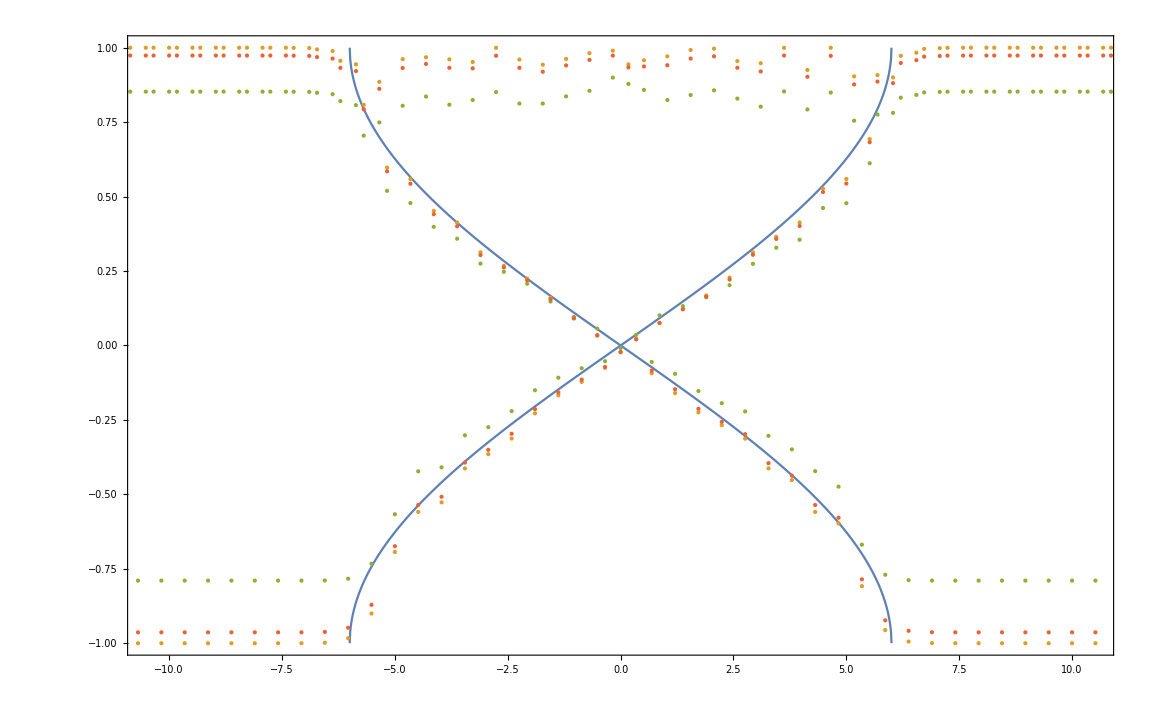

```mathematica
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSizeFolded =Length[Sites]; 
xminFolded=1;
xmaxFolded=SystemSizeFolded;

Sites=XXZ5[[;;,1]];
Sites=Union[Sites];
SystemSizeXXZ5 =Length[Sites]; 
xminXXZ5=1;
xmaxXXZ5=SystemSizeXXZ5;


Sites=XXZ10[[;;,1]];
Sites=Union[Sites];
SystemSizeXXZ10 =Length[Sites]; 
xminXXZ10=1;
xmaxXXZ10=SystemSizeXXZ10;


timestep=0.1;

Time = 5.8;

TimeSlice1 = Time/timestep;
TimeSliceXXZ5 =Time/timestep;
TimeSliceXXZ10 = Time/(timestep (*π/(4 *10.)*));
SHIFT=1;(*technical part:  point types etc *)

radius=0.01;
widht=Thickness[0];
CircleEdgeWidht=Thickness[0.15];
<<MaTeX`

RED0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,Disk[]}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[0,0,0],widht}];



everypoint=1;

DataFolded[l_,time_,col_]:=A[[l+SystemSizeFolded*Floor[time],col]];
ObsFolded[l_,time_]:= 2 DataFolded[l,time,2];

DataXXZ5[l_,time_,col_]:=XXZ5[[l+SystemSizeXXZ5*Floor[time],col]];
ObsXXZ5[l_,time_]:= 4DataXXZ5[l,time,3];

DataXXZ10[l_,time_,col_]:=XXZ10[[l+SystemSizeXXZ10*Floor[time],col]];
ObsXXZ10[l_,time_]:= 4DataXXZ10[l,time,3];


FIG=ListPlot[{
Join[Table[{ζ,2/π ArcSin[ζ/6]},{ζ,-10,10,0.01}],Table[{ζ,-2/π ArcSin[ζ/6]},{ζ,-10,10,0.01}]]
,Table[{(DataFolded[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep), (ObsFolded[l,TimeSlice1])},{l,xminFolded,xmaxFolded,everypoint}]
,Table[{(DataXXZ5[l,TimeSliceXXZ5,1]+SHIFT)/(TimeSliceXXZ5*timestep), (ObsXXZ5[l,TimeSliceXXZ5])},{l,xminXXZ5,xmaxXXZ5,everypoint}]
,Table[{(DataXXZ10[l,TimeSliceXXZ10,1]+SHIFT)/(TimeSliceXXZ10*timestep), (ObsXXZ10[l,TimeSliceXXZ10])},{l,xminXXZ10,xmaxXXZ10,everypoint}]
},
PlotRange->{{-10.5,10.5},{Automatic,Automatic}},
(*AxesLabel -> {"x/t","Spin operator"},*)(*PlotLegends->{"Sx, t="<>ToString[TimeSlice/10],"Sy","Sz"},*)
PlotStyle->PointSize[Medium],

Joined->{True,False,False,False}
,Frame->True,
FrameStyle->BlackFrame,
Axes->{False,False},
BaseStyle->{FontFamily->"Latin Modern Roman"},
FrameLabel->MaTeX[{"\\ell/t","\\langle \\sigma^z_{\\ell}\\sigma^z_{\\ell+1} \\rangle"},FontSize->16],
LabelStyle->Directive[FontSize->12],
PlotLegends->{Placed[MaTeX[{
"Folded (analyt)\\quad \\sigma^z_{\\ell}(t \\to \\infty)"
,"Folded (numerics)\\quad \\sigma^z_{\\ell}\\sigma^z_{\\ell+1}(t="<>ToString[TimeSlice1*timestep]<>")"
,"XXZ-5\\quad \\sigma^z_{\\ell}\\sigma^z_{\\ell+1}(t="<>ToString[TimeSliceXXZ5*timestep]<>")"
,"XXZ-10\\quad \\sigma^z_{\\ell}\\sigma^z_{\\ell+1}(t="<>ToString[TimeSliceXXZ10*timestep]<>")"
},FontSize->8],{0.9,0.6}]}
(*,FrameTicks->{
{{0,0.1,0.2,0.3},None},
{{-6,-4,-2,0,2,4,6},None}}*)

(*,PlotMarkers->{
{BLACK,radius}
,{RED0,radius}
,{BLUE0,radius}
,{RED0, radius}
}*)

 ]
```

```mathematica
Export["../Pictures/Simply_Jammed/XXZ10.pdf",Out[300]];
```

```mathematica
0.01 π/(4.*16)16
```

0.00785398

## XXZ large Delta collapse

```mathematica
(*SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];*)
SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];
A=Import["UUD/N1000/Sz_profile.dat"];
A=Drop[A,1];
𝔸=DeleteCases[A,_?(Length[#]<4&)];
A=Chop[𝔸[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)

(*XXZ=Import["XXZ/Delta5_N363/Sz_profile.dat"];*)
XXZ=Import["XXZ/Delta10_N263/Sz_profile.dat"];
XXZ=Drop[XXZ,1];
XXZ=DeleteCases[XXZ,_?(Length[#]<4&)];
XXZ=Chop[XXZ[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)
```

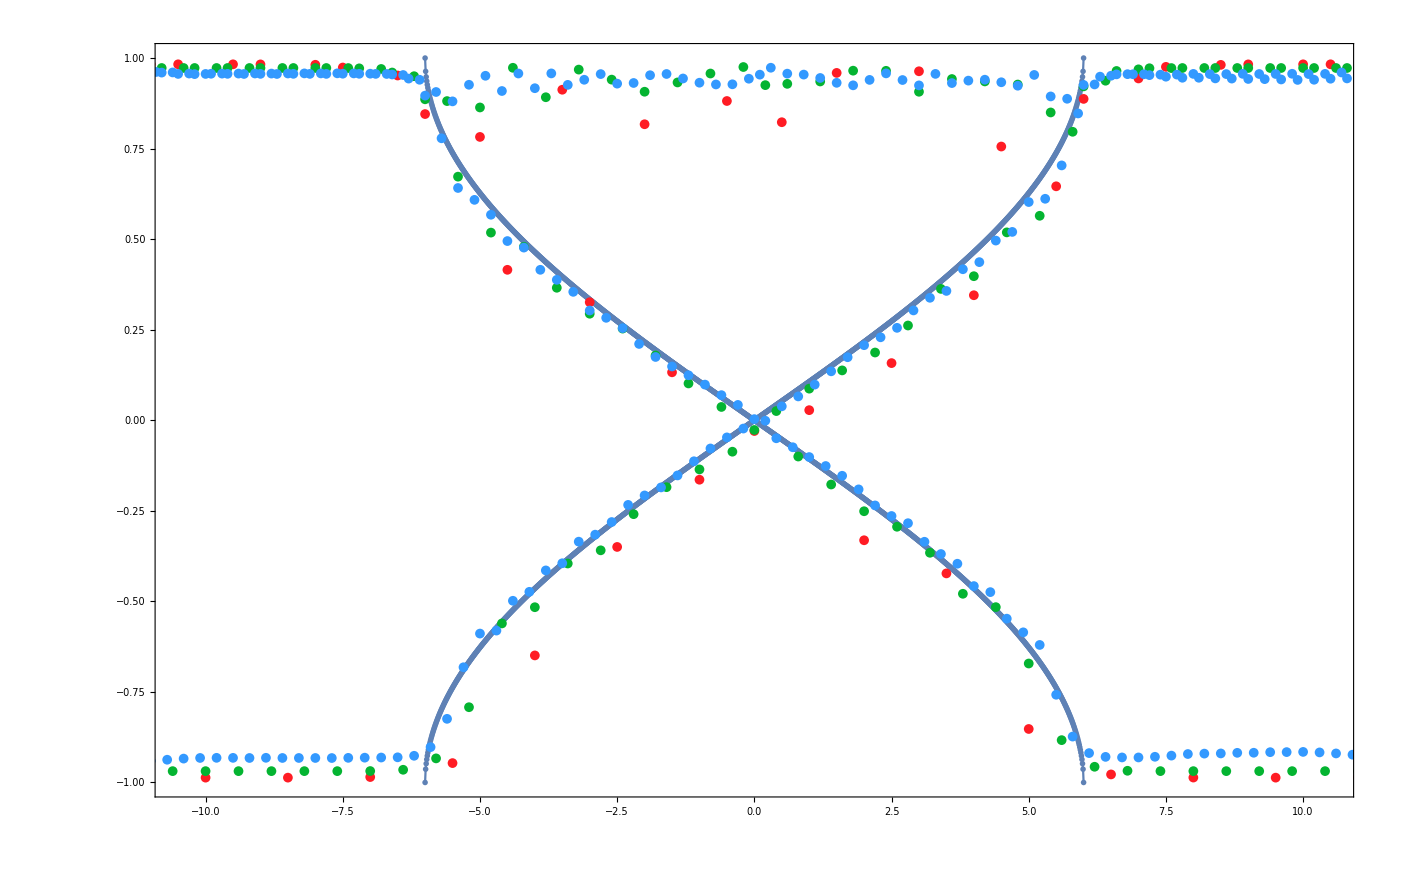

```mathematica
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSizeFolded =Length[Sites]; 
xminFolded=1;
xmaxFolded=SystemSizeFolded;

Sites=XXZ[[;;,1]];
Sites=Union[Sites];
SystemSizeXXZ =Length[Sites]; 
xminXXZ=1;
xmaxXXZ=SystemSizeXXZ;

timestep=0.1;
Time = 10.;

TimeSlice1 = Time/timestep;
TimeSliceXXZ2 =2.0/timestep;
TimeSliceXXZ3 =5.0/timestep;
TimeSliceXXZ4 =Time/timestep;
SHIFT=1;(*technical part:  point types etc *)

radius=10.;
width=Thickness[0];
CircleEdgeWidht=Thickness[0.15];
<<MaTeX`

RED0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[1,0.11,0.14],width,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],width,Disk[]}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],width,Disk[]}];
BLACK0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[0,0,0],width,Disk[]}];



everypoint=1;

DataFolded[l_,time_,col_]:=A[[l+SystemSizeFolded*Floor[time],col]];
ObsFolded[l_,time_]:= 2 DataFolded[l,time,2];

DataXXZ[l_,time_,col_]:=XXZ[[l+SystemSizeXXZ*Floor[time],col]];
ObsXXZ[l_,time_]:= 4DataXXZ[l,time,3];


FIG=ListPlot[{
Join[Table[{ζ,2/π ArcSin[ζ/6]},{ζ,-10,10,0.01}],Table[{ζ,-2/π ArcSin[ζ/6]},{ζ,-10,10,0.01}]]
(*,Table[{(DataFolded[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep), (ObsFolded[l,TimeSlice1])},{l,xminFolded,xmaxFolded,everypoint}]*)
,Table[{(DataXXZ[l,TimeSliceXXZ2,1]+SHIFT)/(TimeSliceXXZ2*timestep), (ObsXXZ[l,TimeSliceXXZ2])},{l,xminXXZ,xmaxXXZ,everypoint}]
,Table[{(DataXXZ[l,TimeSliceXXZ3,1]+SHIFT)/(TimeSliceXXZ3*timestep), (ObsXXZ[l,TimeSliceXXZ3])},{l,xminXXZ,xmaxXXZ,everypoint}]
,Table[{(DataXXZ[l,TimeSliceXXZ4,1]+SHIFT)/(TimeSliceXXZ4*timestep), (ObsXXZ[l,TimeSliceXXZ4])},{l,xminXXZ,xmaxXXZ,everypoint}]
},
PlotRange->{{-10.5,10.5},{Automatic,Automatic}},
(*AxesLabel -> {"x/t","Spin operator"},*)(*PlotLegends->{"Sx, t="<>ToString[TimeSlice/10],"Sy","Sz"},*)
PlotStyle->PointSize[Medium],

Joined->{True,False,False,False}
,Frame->True,
FrameStyle->BlackFrame,
Axes->{False,False},
BaseStyle->{FontFamily->"Latin Modern Roman"},
FrameLabel->MaTeX[{"\\ell/t","\\langle \\sigma^z_{\\ell}\\sigma^z_{\\ell+1} \\rangle"},FontSize->16],
LabelStyle->Directive[FontSize->12],
PlotLegends->{Placed[MaTeX[{
"Folded (analyt)\\quad \\sigma^z_{\\ell}(t \\to \\infty)"
(*,"Folded (numerics)\\quad \\sigma^z_{\\ell}(t="<>ToString[TimeSlice1*timestep]<>")"*)
,"XXZ-10\\quad \\sigma^z_{\\ell}\\sigma^z_{\\ell+1}(t="<>ToString[TimeSliceXXZ2*timestep]<>")"
,"XXZ-10\\quad \\sigma^z_{\\ell}\\sigma^z_{\\ell+1}(t="<>ToString[TimeSliceXXZ3*timestep]<>")"
,"XXZ-10\\quad \\sigma^z_{\\ell}\\sigma^z_{\\ell+1}(t="<>ToString[TimeSliceXXZ4*timestep]<>")"
},FontSize->20],{0.85,0.5}]}
(*,FrameTicks->{
{{0,0.1,0.2,0.3},None},
{{-6,-4,-2,0,2,4,6},None}}*)

,PlotMarkers->{
{BLACK,radius}
(*,{BLACK0,radius}*)
,{RED0,radius}
,{GREEN0,radius}
,{BLUE0, radius}
}

 ]
```

```mathematica
Export["../Pictures/Simply_Jammed/XXZ10.pdf",Out[300]];
```

```mathematica
0.01 π/(4.*16)16
```

0.00785398

## Folded collapse with a scaling curve

```mathematica
(*SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];*)
SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];
A=Import["UUD/N2000/Sz_profile.dat"];
A=Drop[A,1];
𝔸=DeleteCases[A,_?(Length[#]<4&)];
A=Chop[𝔸[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)
```

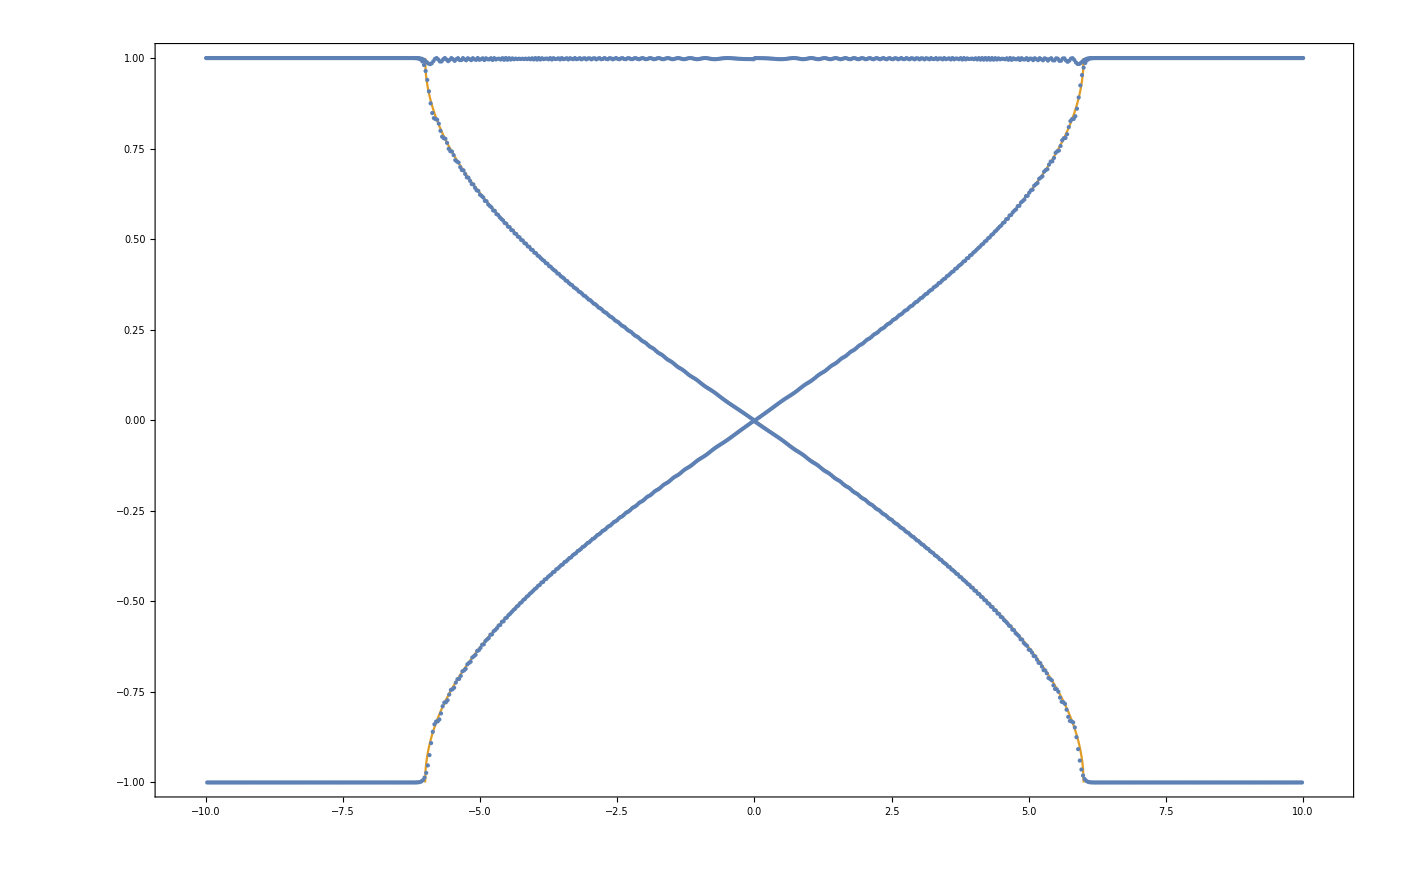

```mathematica
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSizeFolded =Length[Sites]; 
xminFolded=1;
xmaxFolded=SystemSizeFolded;

timestep=0.1;
Time = 100;

TimeSlice1 = Time/timestep;
SHIFT=1;(*technical part:  point types etc *)

radius=0.01;
width=Thickness[0];
CircleEdgeWidht=Thickness[0.15];
<<MaTeX`

RED0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[1,0.11,0.14],width,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],width,Disk[]}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],width,Disk[]}];
BLACK0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[0,0,0],width,Disk[]}];



everypoint=1;

DataFolded[l_,time_,col_]:=A[[l+SystemSizeFolded*Floor[time],col]];
ObsFolded[l_,time_]:= 2 DataFolded[l,time,2];

FIG=ListPlot[{

Table[{(DataFolded[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep), (ObsFolded[l,TimeSlice1])},{l,xminFolded,xmaxFolded,everypoint}]
,Join[Table[{ζ,2/π ArcSin[ζ/6]},{ζ,-10,10,0.01}],Table[{ζ,-2/π ArcSin[ζ/6]},{ζ,-10,10,0.01}]]
},
PlotRange->{{-10.5,10.5},{Automatic,Automatic}},
(*AxesLabel -> {"x/t","Spin operator"},*)(*PlotLegends->{"Sx, t="<>ToString[TimeSlice/10],"Sy","Sz"},*)
PlotStyle->PointSize[Medium],

Joined->{False,True}
,Frame->True,
FrameStyle->BlackFrame,
Axes->{False,False},
BaseStyle->{FontFamily->"Latin Modern Roman"},
FrameLabel->MaTeX[{"\\xi=\\ell/t","\\langle \\sigma^z_{\\ell} \\rangle"},FontSize->25],
LabelStyle->Directive[FontSize->15],
PlotLegends->{Placed[MaTeX[{
"Folded (numerics)\\quad \\sigma^z_{\\ell}(t="<>ToString[TimeSlice1*timestep]<>")"
,"Folded (analytics)\\quad \\sigma^z_{\\ell}(t \\to \\infty)"

},FontSize->20],{0.85,0.5}]}
(*,FrameTicks->{
{{0,0.1,0.2,0.3},None},
{{-6,-4,-2,0,2,4,6},None}}*)

(*,PlotMarkers->{
(*,{BLACK0,radius}*)
{RED0,radius}
,{GREEN0,radius}
,{BLUE0, radius}
}*)

 ]
```

```mathematica
Export["../Pictures/Simply_Jammed/XXZ10.pdf",Out[300]];
```

```mathematica
0.01 π/(4.*16)16
```

0.00785398

## Jamming criterium ⟨(1-(σ^z)_l)/2(1-(σ^z)_(l+1))/2⟩≡[⟨(σ^z)_l(σ^z)_(l+1)⟩ – ⟨(σ^z)_l⟩-⟨(σ^z)_(l+1)⟩ ++1 ]/4 Profile

```mathematica
<<MaTeX`
SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];
(*SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];*)
A=Import["UUD/N1000/Sz_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
```

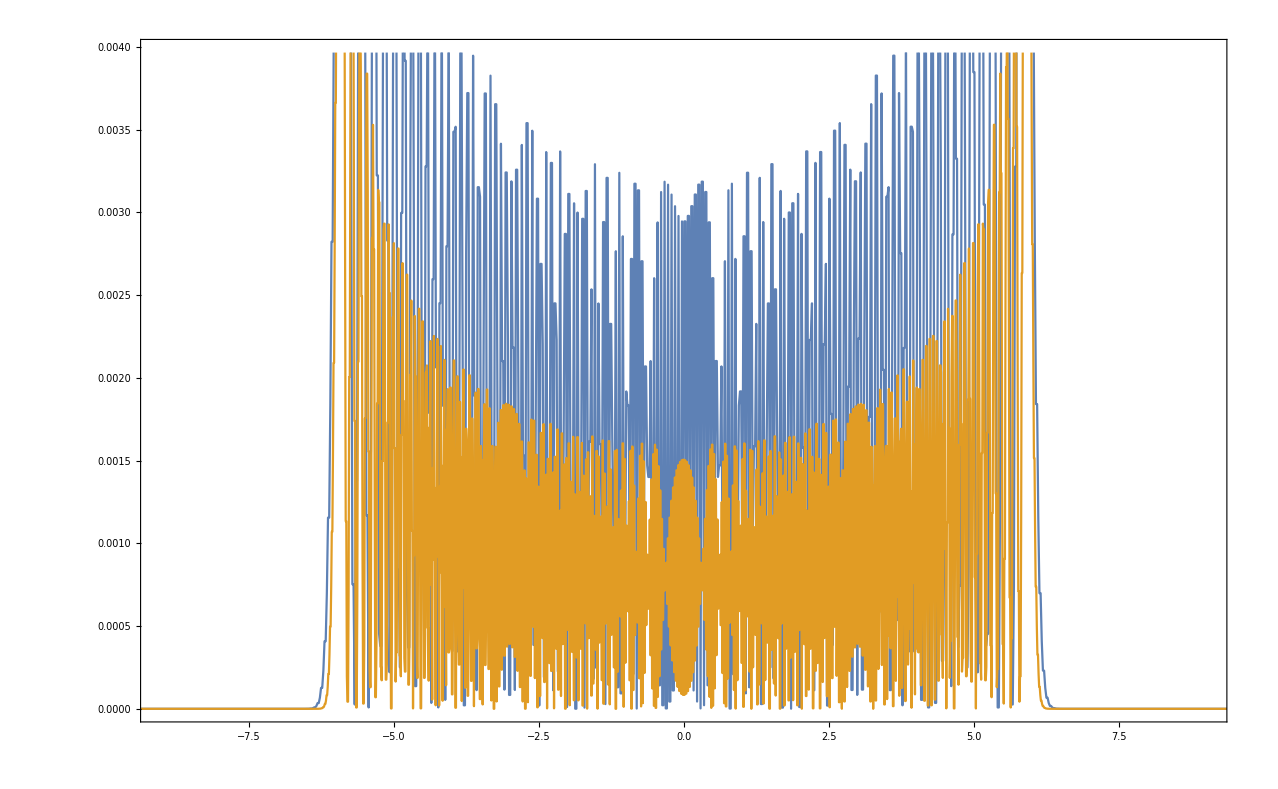

```mathematica
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)


SHIFT=1.5; (*To match 0 in data with 0 on the plot*)
timestep=0.1(*0.011193*);
TimeSlice0=10;
TimeSlice1=10/timestep;
TimeSlice2=50/timestep;
TimeSlice3=100/timestep;

radius=0.01;
widht=Thickness[0.002];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];

Sigma[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
Obs[n_,time_]:=(timestep time)^(0.0)( 4Sigma[n,3,time]  -2(Sigma[n+1,2,time] +Sigma[n,2,time])  + 1)/4;
FIG=ListPlot[{

Table[{(A[[n+SystemSize*Floor[TimeSlice2],1]]+SHIFT)/(TimeSlice2*timestep),Obs[n,TimeSlice2]},{n,xmin,xmax,1}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin,xmax,1}]


},
Joined->True
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"\\xi=\\ell/t","\\mathcal{P}_{\\downarrow \\downarrow}(\\ell/t)"},FontSize->16]

(*\\langle \\frac{1-\\sigma^z_{\\ell}}{2}\\frac{1-\\sigma^z_{\\ell+1}}{2} \\rangle*)
,LabelStyle->Directive[FontSize->12]
,LABELS={
"t="<>ToString[TimeSlice2*timestep]
(*,"t="<>ToString[TimeSlice2*timestep]*)
,"t="<>ToString[TimeSlice3*timestep]
};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 12],{0.95,0.5}]
,PlotRange->{{-9,9},{Automatic,Automatic}}
(*,FrameTicks->{
{{0,{0.02,""},{0.04,""},{0.06,""},{0.08,""}
,0.1,{0.12,""},{0.14,""},{0.16,""},{0.18,""}
,0.2,{0.22,""},{0.24,""},{0.26,""},{0.28,""}
,0.3},None},
{(*{-6,-4,-2,0,2,4,6}*)Automatic,None}}*)
(*PlotStyle->{RGBColor[1,0.11,0.14],RGBColor[4/255,180/255,49/255],RGBColor[51/255,153/255,1]},*)
(*,PlotMarkers->{
(*{BLACK,0.25radius},*)
{BLUE0,radius},
(*{GREEN0,radius},*)
{RED0, radius}
}*)

 ]
```

{k→0.0606857}

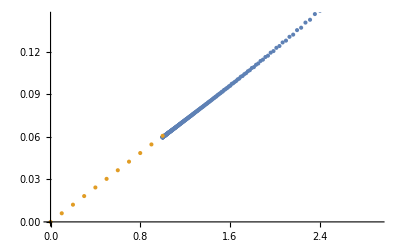

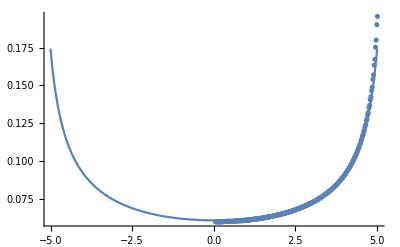

```mathematica
Experim=Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,Floor[(xmax-xmin)/2]+3,xmax-100}];
ExperimGamma = Table[{1/√(1-(3./16 Experim[[l,1]])^2),Experim[[l,2]]},{l,1,Floor[1*Length[Experim]]}];
FIT =FindFit[ExperimGamma,k x,{k},x]

ListPlot[{ExperimGamma,Table[{l,(k/.FIT)l},{l,0,1,0.1}]
}]
Show[
Plot[(k/.FIT)/√(1-(3/16 x)^2) ,{x,-5,5},PlotRange->All]
,ListPlot[Experim]
]
```

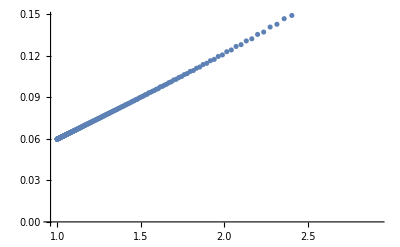

```mathematica
ExperimGamma = Table[{1/√(1-(3./16 Experim[[l,1]])^2),Experim[[l,2]]},{l,1,Length[Experim]}];
ListPlot[ExperimGamma]
```

```mathematica
Export["~/Programs/Folded_XXZ_GS/code/Pictures/For_paper/Mathematica.pdf",FIG];
```

## Jamming criterium term by term≡[⟨(σ^z)_l(σ^z)_(l+1)⟩ – ⟨(σ^z)_l⟩-⟨(σ^z)_(l+1)⟩ ++1 ]/4 Profile

```mathematica
<<MaTeX`
SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];
(*SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];*)
A=Import["UUD/N1000/Sz_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
```

```mathematica
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)
timestep=0.1(*0.011193*);
TimeSlice0=10;
TimeSlice2=50/timestep;

radius=0.01;
widht=Thickness[0.002];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];

Sigma[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
Obs[n_,time_]:=(timestep time)^(0.0)(4Sigma[n,3,time]  -2(Sigma[n+1,2,time] +Sigma[n,2,time])  + 1)/4;
FIG=ListPlot[{

Table[{(A[[n+SystemSize*Floor[TimeSlice2],1]]+SHIFT)/(TimeSlice2*timestep),Sigma[n,2,TimeSlice2]},{n,xmin,xmax,1}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice2],1]]+SHIFT)/(TimeSlice2*timestep),Sigma[n+1,2,TimeSlice2]},{n,xmin,xmax,1}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice2],1]]+SHIFT)/(TimeSlice2*timestep),(Sigma[n,2,TimeSlice2]+Sigma[n+1,2,TimeSlice2])},{n,xmin,xmax,1}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice2],1]]+SHIFT)/(TimeSlice2*timestep),Obs[n,TimeSlice2]},{n,xmin,xmax,1}]

},
Joined->False
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"\\xi=\\ell/t","\\sigma^z(t)"},FontSize->16]

(*\\langle \\frac{1-\\sigma^z_{\\ell}}{2}\\frac{1-\\sigma^z_{\\ell+1}}{2} \\rangle*)
,LabelStyle->Directive[FontSize->12]
,LABELS={
"\\sigma^z_{\\ell},t="<>ToString[TimeSlice2*timestep]
(*,"t="<>ToString[TimeSlice2*timestep]*)
,"\\sigma^z_{\\ell+1}, t="<>ToString[TimeSlice2*timestep]

,"\\sigma^z_{\\ell}+\\sigma^z_{\\ell+1}, t="<>ToString[TimeSlice2*timestep]
,"\\sigma^z_{\\ell}*\\sigma^z_{\\ell+1}, t="<>ToString[TimeSlice2*timestep]
};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 20],{1.,0.5}]
,PlotRange->{{-9,9},{Automatic,Automatic}}
(*,FrameTicks->{
{{0,{0.02,""},{0.04,""},{0.06,""},{0.08,""}
,0.1,{0.12,""},{0.14,""},{0.16,""},{0.18,""}
,0.2,{0.22,""},{0.24,""},{0.26,""},{0.28,""}
,0.3},None},
{(*{-6,-4,-2,0,2,4,6}*)Automatic,None}}*)
(*PlotStyle->{RGBColor[1,0.11,0.14],RGBColor[4/255,180/255,49/255],RGBColor[51/255,153/255,1]},*)
(*,PlotMarkers->{
(*{BLACK,0.25radius},*)
{BLUE0,radius},
(*{GREEN0,radius},*)
{RED0, radius}
}*)

 ]
```

-Graphics-

```mathematica
Experim=Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,Floor[(xmax-xmin)/2]+3,xmax-100}];
ExperimGamma = Table[{1/√(1-(3./16 Experim[[l,1]])^2),Experim[[l,2]]},{l,1,Floor[1*Length[Experim]]}];
FIT =FindFit[ExperimGamma,k x,{k},x]

ListPlot[{ExperimGamma,Table[{l,(k/.FIT)l},{l,0,1,0.1}]
}]
Show[
Plot[(k/.FIT)/√(1-(3/16 x)^2) ,{x,-5,5},PlotRange->All]
,ListPlot[Experim]
]
```

{k→0.0606857}

-Graphics-

-Graphics-

```mathematica
ExperimGamma = Table[{1/√(1-(3./16 Experim[[l,1]])^2),Experim[[l,2]]},{l,1,Length[Experim]}];
ListPlot[ExperimGamma]
```

-Graphics-

```mathematica
Export["~/Programs/Folded_XXZ_GS/code/Pictures/For_paper/Mathematica.pdf",FIG];
```

## Saverio for <Sx_i Sy_(i+2)>

```mathematica
S[l_,t_]:=Sum[BesselJ[k,4 t]^2,{k,l+1,200}]-1/2;
Zplus3Z[t_]:=-1+KroneckerDelta[b,m-1]+KroneckerDelta[b,m]+2 If[a<m,BesselJ[l-a,4 t]^2 (1-2 KroneckerDelta[b,m]),0]+2 If[a+1>=m,BesselJ[l-a-1,4 t]^2 (1-2 KroneckerDelta[b,m-1]),0]+2 S[l-m,t] (KroneckerDelta[b,m]-KroneckerDelta[b,m-1])/. {a->4, b->3,m->4,l->1};

Sav=Table[{t,Zplus3Z[t]},{t,0,10,0.01}];
```

General::munfl: (5.58352×10^-157)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.10699×10^-160)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.80366×10^-164)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

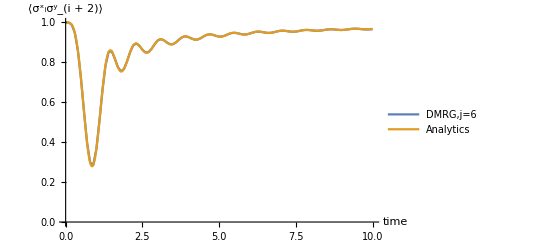

```mathematica
SetDirectory["~/3siteHam/Folded_XXZ_GS/"];
(*Data=Import["Data/Sav/DownUpUp/Correlation3.dat"];*)

Data=Import["Data/Sav/DownUpUp/Sz_profile.dat"];
Data=Drop[Data,1];
Data=DeleteCases[Data,_?(Length[#]<4&)];
column =2;

site=6;
shift=0;
flippedspin=3;
sign=Sign[r-flippedspin];
Data=Cases[Data,_?(#[[1]]==0+site&)];Data=Data[[;;,{8,column}]];
ZZ[t_,r_]:=1-2 (If[r-d<m,BesselJ[l-r+d,4 t]^2,0]+If[r+1>=m+d,BesselJ[l-r+d-1,4 t]^2,0]+If[m>r,BesselJ[l-r,4 t]^2,0]+If[m<=r+1,BesselJ[l-r-1,4 t]^2,0])/. {m->4,l->1,d->1};
XY[t_,r_]:=If[r<m,2 Cos[(1-d) Pi/2] BesselJ[l-r,4 t] BesselJ[l-r+d,4 t],0]+If[r>=m+d-1,2 Cos[(1-d) Pi/2] BesselJ[l-r-1,4 t] BesselJ[l-r+d-1,4 t],0]/. {m->4,l->1,d->1};
Z[t_,r_]:=1-2 HeavisideTheta[m-r-1/2] BesselJ[l-r,4 t]^2-2 HeavisideTheta[r+1-m+1/2] BesselJ[l-r-1,4 t]^2/.{m->4, l->1};




ListLinePlot[{Table[{Data[[k,1]],2Data[[k,2]]},{k,1,Length[Data]}]
(*,Table[{t,2BesselJ[-r-1Sign[r-flippedspin],4t]BesselJ[-r,4t]},{t,0,10,0.01}]*)
,Table[{t,Z[t,site/2]},{t,0,10,0.01}]
(*Sav*)

},PlotRange -> All,PlotLegends->{"DMRG,j="<>ToString[0+site],"Analytics"},AxesLabel -> {"time","⟨(σ^x)_i(σ^y)_(i + 2)⟩"}]
```

```mathematica
Export["~/Programs/Folded_XXZ_GS/code/Sx0.dat",b]
```

~/Programs/Folded_XXZ_GS/code/Sx0.dat

```mathematica
a[[2,1]]
```

0.1

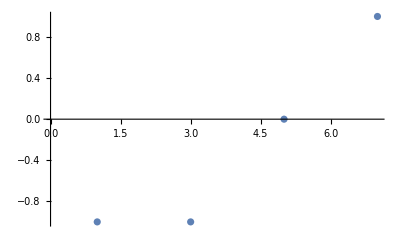

```mathematica
Dots={{0,0},{2,0},{5,0},{7,1}};
ListPlot[Dots]
```

```mathematica
1/(4/(π 6.))
```

4.71239

```mathematica
-0.95-458.6-40.00-80.00-0.09-45.59
```

-625.23

## Saverio Ising

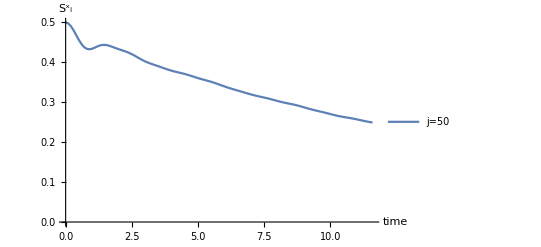

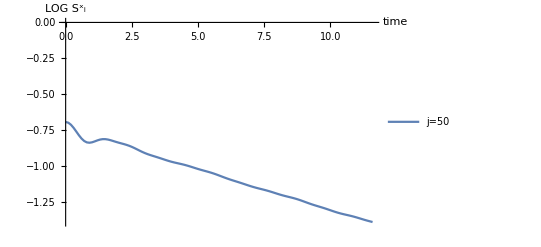

```mathematica
A=Import["~/Programs/Folded_XXZ_GS/Data/Ising/h0.5/SxSySz_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
column =2;
site=50;
𝔸=Cases[A,_?(#[[1]]==0+site&)];a=𝔸[[;;,{6,column}]];

ListLinePlot[{
Table[{a[[i,1]],a[[i,2]]},{i,1,Length[a]}]

},PlotRange -> All,PlotLegends->{"j="<>ToString[0+site]},AxesLabel -> {"time","(S^x)_i"}]

ListLinePlot[{
Table[{a[[i,1]],Log[a[[i,2]]]},{i,1,Length[a]}]

},PlotRange -> All,PlotLegends->{"j="<>ToString[0+site]},AxesLabel -> {"time","LOG (S^x)_i"}]
```

```mathematica
a[[2,2]]
```

0.497535

~/Programs/Folded_XXZ_GS/code/Sx0.dat

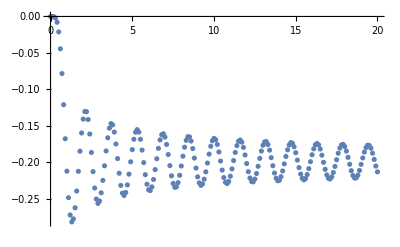

```mathematica
Export["~/Programs/Folded_XXZ_GS/code/Sx0.dat",b]
```